```mathematica
Quit[]
```

```mathematica
C1=1;C2=2;C3=3;C4=4;C5=5;C6=6;R1=1;R2=1;
A=({{1/R1+s*C1+s*C5, -s*C5, -s*C1, 0}, {-s*C5, s*C5+s*C2+1/R2, 0, -s*C2}, {-s*C1, 0, s*C1+s*C3+s*C6, -s*C6}, {0, -s*C2, -s*C6, s*C6+s*C4+s*C2}})
```

{{1+6 s,-5 s,-s,0},{-5 s,1+7 s,0,-2 s},{-s,0,10 s,-6 s},{0,-2 s,-6 s,12 s}}

```mathematica
B=({{E1/R1}, {0}, {0}, {0}})
```

{{E1},{0},{0},{0}}

```mathematica
LinearSolve[A,B]
```

{{(E1 (21+137 s))/(21+260 s+247 s^2)},{(108 E1 s)/(21+260 s+247 s^2)},{(E1 (3+35 s))/(21+260 s+247 s^2)},{(E1 (3+71 s))/(2 (21+260 s+247 s^2))}}

```mathematica
((0.554655870445344 E1 (0.15483300154833002+1. s))/(0.08587903324745431+1.057661636609005 s+1. s^2))/((0.437246963562753 E1 s)/(0.08587903324745431+1.057661636609005 s+1. s^2))
```

(1.26852 (0.154833+1. s))/s

```mathematica
InverseLaplaceTransform[(1.2685185185185184 (0.15483300154833002+1. s))/s,s,t]
```

1.26852 (0.154833+1. DiracDelta[t])

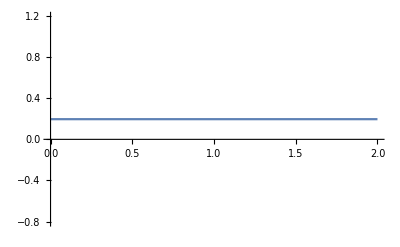

```mathematica
Plot[1.2685185185185184 *(0.15483300154833002+1. DiracDelta[t]),{t,0,2},PlotRange->All]
```

```mathematica
Quit[]
```

```mathematica
C1=0.1;C2=0.1;C3=0.1;C4=0.1;C5=0.1;R1=1;R2=1;R3=1;R4=1;R5=1;
```

```mathematica
A=({{1/R1+s*C1+1/R2, -1/R2, 0, 0, 0}, {-1/R1, 1/R2+s*C2+1/R3, -1/R3, 0, 0}, {0, -1/R3, 1/R3+s*C3+1/R4, -1/R4, 0}, {0, 0, -1/R4, 1/R4+s*C4+1/R5, -1/R5}, {0, 0, 0, -1/R5, 1/R5+s*C5}})
```

{{2+0.1 s,-1,0,0,0},{-1,2+0.1 s,-1,0,0},{0,-1,2+0.1 s,-1,0},{0,0,-1,2+0.1 s,-1},{0,0,0,-1,1+0.1 s}}

```mathematica
B=({{E1/R1}, {0}, {0}, {0}, {0}})
```

{{E1},{0},{0},{0},{0}}

```mathematica
tensiones=LinearSolve[A,B]
```

{{(10. E1 (10000.+10000. s+1500. s^2+70. s^3+1. s^4))/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)},{(100. E1 (1000.+600. s+50. s^2+1. s^3))/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)},{(1000. E1 (100.+30. s+1. s^2))/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)},{(10000. E1 (10.+1. s))/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)},{(100000. E1)/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)}}

```mathematica
salida=Extract[tensiones,{5,1}]/Extract[tensiones,{1,1}]
```

10000./(10000.+10000. s+1500. s^2+70. s^3+1. s^4)

```mathematica
tempo[t_]=Simplify[InverseLaplaceTransform[salida,s,t]]
```

-0.977095 ⅇ^(-35.3209 t)+2.81343 ⅇ^(-23.473 t)-3.33333 ⅇ^(-10. t)+1.497 ⅇ^(-1.20615 t)

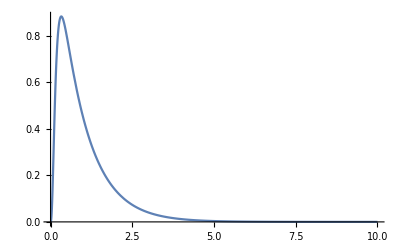

```mathematica
Plot[tempo[t],{t,0,10}, PlotRange->All]
```

```mathematica
modelo=TransferFunctionModel[salida,s]
```

10000./(10000.+10000. s+1500. s^2+70. s^3+1. s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s119999.9999999999989999.9999999999961FalseFalseFalseAutomaticNoneAutomatic